```mathematica
x1=-0.2;h=0.076;n=24;
```

```mathematica
Array[xdata,n,0];Array[ydata,n,0];
```

```mathematica
ydata[0]=0.0398739;
```

```mathematica
ydata[1]=0.0151449;
```

```mathematica
ydata[2]=0.00232526;
```

```mathematica
ydata[3]=0.000775957;
```

```mathematica
ydata[4]=0.010885;
```

```mathematica
ydata[5]=0.0317362;
```

```mathematica
ydata[6]=0.0647997;
```

```mathematica
ydata[7]=0.105358;
```

```mathematica
ydata[8]=0.159633;
```

```mathematica
ydata[9]=0.215989;
```

```mathematica
ydata[10]=0.288732;
```

```mathematica
ydata[11]=0.356672;
```

```mathematica
ydata[12]=0.444944;
```

```mathematica
ydata[13]=0.520637;
```

```mathematica
ydata[14]=0.621813;
```

```mathematica
ydata[15]=0.702119;
```

```mathematica
ydata[16]=0.814088;
```

```mathematica
ydata[17]=0.89659;
```

```mathematica
ydata[18]=1.01775;
```

```mathematica
ydata[19]=1.10065;
```

```mathematica
ydata[20]=1.22983;
```

```mathematica
ydata[21]=1.31182;
```

```mathematica
ydata[22]=1.44816;
```

```mathematica
ydata[23]=1.52829;
```

```mathematica
ydata[24]=1.67119;
```

```mathematica
For[i=0,i<=n,i++,
xdata[i]=x1+h*i;];
```

```mathematica
MatrixForm[Table[{xdata[i],ydata[i]},{i,0,n}]]
```

(-0.2 | 0.0398739
-0.124 | 0.0151449
-0.048 | 0.00232526
0.028 | 0.000775957
0.104 | 0.010885
0.18 | 0.0317362
0.256 | 0.0647997
0.332 | 0.105358
0.408 | 0.159633
0.484 | 0.215989
0.56 | 0.288732
0.636 | 0.356672
0.712 | 0.444944
0.788 | 0.520637
0.864 | 0.621813
0.94 | 0.702119
1.016 | 0.814088
1.092 | 0.89659
1.168 | 1.01775
1.244 | 1.10065
1.32 | 1.22983
1.396 | 1.31182
1.472 | 1.44816
1.548 | 1.52829
1.624 | 1.67119)

```mathematica
data25=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
```

```mathematica
inpln25:=InterpolatingPolynomial[data25,x];
```

```mathematica
Collect[inpln25,x]
```

-2.22799+94.0749 x+212.059 x^2-37304.5 x^3+437690. x^4-811591. x^5-2.11444×10^7 x^6+2.03249×10^8 x^7-7.65239×10^8 x^8+1.0944×10^8 x^9+1.33233×10^10 x^10-7.6532×10^10 x^11+2.56728×10^11 x^12-6.09543×10^11 x^13+1.09134×10^12 x^14-1.5156×10^12 x^15+1.65365×10^12 x^16-1.42262×10^12 x^17+9.61369×10^11 x^18-5.04665×10^11 x^19+2.01625×10^11 x^20-5.92363×10^10 x^21+1.20642×10^10 x^22-1.52124×10^9 x^23+8.94467×10^7 x^24

```mathematica
inplnPlot:=Plot[inpln25,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

```mathematica
pointsPlot:=ListPlot[data25,PlotStyle->Red, PlotLegends->"начальное значение"];
```

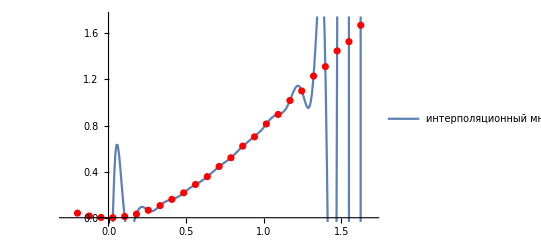

```mathematica
Show[{inplnPlot,pointsPlot}]
```

```mathematica
data12=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,2}];
inpln12:=InterpolatingPolynomial[data12,x];Collect[inpln12,x]
```

6.52815×10^-7+1.65928×10^-6 x+1.00981 x^2+0.00124675 x^3-0.336616 x^4-0.0254985 x^5+0.30409 x^6-0.17636 x^7-0.0320428 x^8+0.0753244 x^9-0.0308897 x^10+0.00407853 x^11+0.000106787 x^12

```mathematica
inplnPlot12:=Plot[inpln12,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

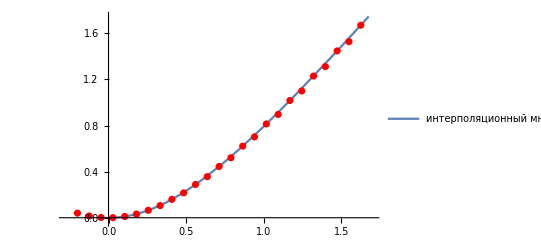

```mathematica
Show[{inplnPlot12,pointsPlot}]
```

```mathematica
data8=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,3}];
```

```mathematica
inpln8:=InterpolatingPolynomial[data8,x];Collect[inpln8,x]
```

-0.00627137+0.250053 x+0.148586 x^2-3.86945 x^3+24.6612 x^4-50.9771 x^5+49.6364 x^6-23.3224 x^7+4.25796 x^8

```mathematica
inplnPlot8:=Plot[inpln8,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

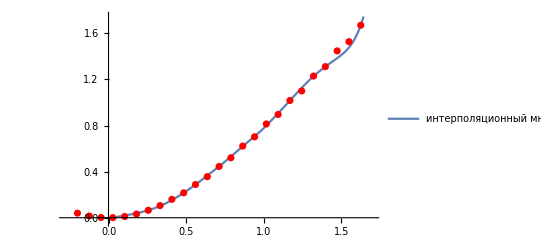

```mathematica
Show[{inplnPlot8,pointsPlot}]
```

```mathematica
data5=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,6}];
```

```mathematica
inpln5:=InterpolatingPolynomial[data5,x];Collect[inpln5,x]
```

-0.0054159+0.0124854 x+1.11672 x^2-0.380003 x^3+0.0486935 x^4

```mathematica
inplnPlot5:=Plot[inpln5,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

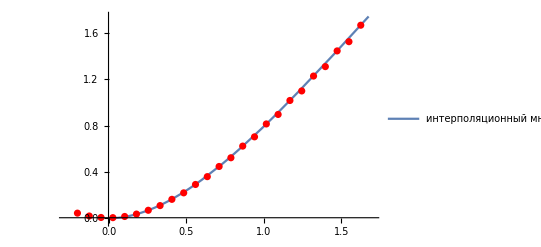

```mathematica
Show[{inplnPlot5,pointsPlot}]
```

```mathematica
spln25:=Interpolation[data25,Method->"Spline"];
```

```mathematica
splnPlot25:=Plot[{spln25[x]},{x,xdata[0]-h,xdata[n]+h},PlotLegends->{"сплайн"},PlotStyle->Green,PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}]
```

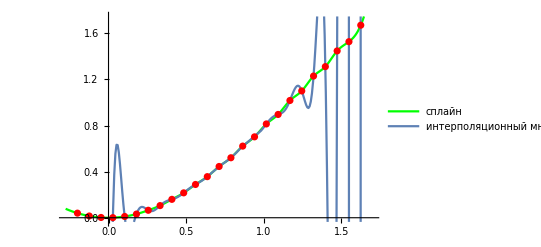

```mathematica
Show[{splnPlot25,inplnPlot,pointsPlot}]
```

```mathematica
spln12:=Interpolation[data12,Method->"Spline"];
```

```mathematica
splnPlot12:=Plot[{spln12[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

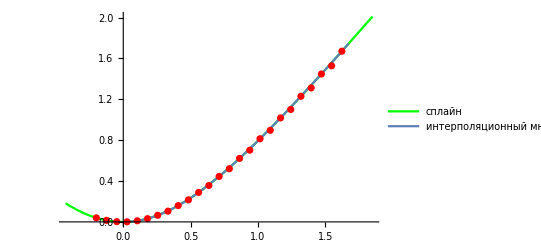

```mathematica
Show[{splnPlot12,inplnPlot12,pointsPlot}]
```

```mathematica
spln8:=Interpolation[data8,Method->"Spline"];
```

```mathematica
splnPlot8:=Plot[{spln8[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

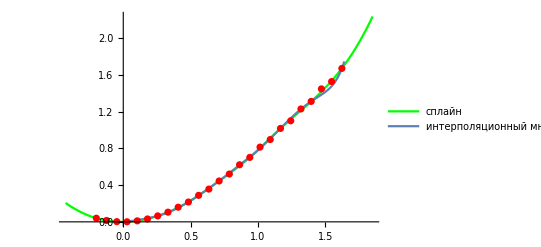

```mathematica
Show[{splnPlot8,inplnPlot8,pointsPlot}]
```

```mathematica
spln5:=Interpolation[data5,Method->"Spline"];
```

```mathematica
splnPlot5:=Plot[{spln5[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

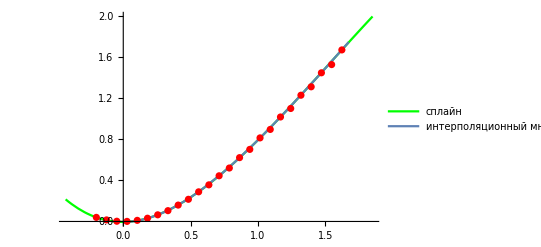

```mathematica
Show[{splnPlot5,inplnPlot5,pointsPlot}]
```

```mathematica
Clear[a,b]
```

```mathematica
rules1=FindFit[data25,a+b*x,{a,b},x];
```

```mathematica
y1=a+b*x/.rules1
f1[x_]:=a+b*x/.rules1;
```

-0.095523+0.954375 x

```mathematica
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
```

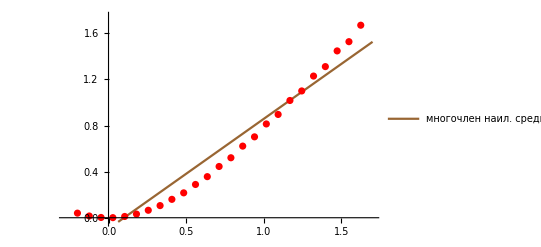

0.45712

```mathematica
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
Clear[a,b]
```

0.0058927+0.255336 x+0.490899 x^2

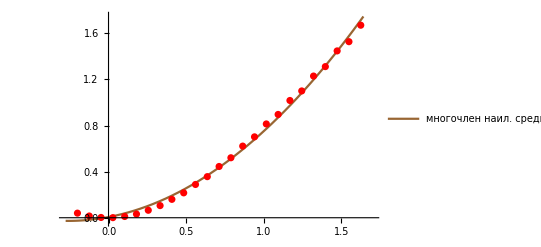

0.0244251

```mathematica
rules1=FindFit[data25,a+b*x+c*x*x,{a,b,c},x];
y1=a+b*x+c*x*x/.rules1
f1[x_]:=a+b*x+c*x*x/.rules1;
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
∑_(i=0)^(n-1) ydata[i]*(xdata[i+1]-xdata[i])
∑_(i=1)^n ydata[i]*(xdata[i]-xdata[i-1])
∑_(i=0)^(n-1) (ydata[i]+ydata[i+1])/2(xdata[i+1]-xdata[i])
h/3*(ydata[0]+ydata[n]+4*∑_(i=1)^(n/2) ydata[2*i-1]+2*∑_(i=1)^(n/2-1) ydata[2*i])
```

0.982575

1.10655

1.04456

1.04019